## Load packages

### Add notebook directory to package path

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

### Initialize

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<PlotMatexFormatting`;
```

```mathematica
<<ExtFileLoading`;
```

```mathematica
<<ArrayManip`;
```

```mathematica
<<FileNaming`;
```

```mathematica
<<StrIOManip`;
```

```mathematica
<<FileSaving`;
```

```mathematica
<<MCLoops`;
```

```mathematica
<<Geo3d`;
```

### Reload external evaluators

```mathematica
<<"ExternalEvaluatorLoad.wl"
```

```mathematica
(*<<"ExternalEvaluateJulia`"*)
```

### Check directory

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules

### Check path

```mathematica
$Path
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

## File name constants

### Reading

```mathematica
dirLog="./log/";
```

```mathematica
dirFigs="./figs/";
```

```mathematica
dirFigsDoc="./figs/figsDoc/";
```

```mathematica
fNameFLstLstJld2="fNameFileLstJld2Lst.txt";
fNameFLstLst="fNameFileLstLst.txt";
fNameSaveParamLstLst="fNameSaveParamsLst.txt";
```

```mathematica
numDigs=3;
```

### Saving

```mathematica
fNameFigLstTmp="fNameFigLstTmp.txt";
```

## Plotting options

```mathematica
markerStyleLstTmp=markerStyleLstFunc[colorLst,AbsolutePointSize[4]];
```

```mathematica
markerStyleLstLine=markerStyleLstFunc[colorLst,AbsolutePointSize[2]];
```

```mathematica
markerStyleLstOpac=markerStyleLstFunc[Opacity[0.3,#]&/@colorLst,AbsolutePointSize[3]];
```

## Functions

```mathematica
nDim3=3;
```

### Rotation matrix formulas

```mathematica
uVectLst3=Table[If[#==dim,1,0]&/@Range[nDim3],{dim,nDim3}];
```

```mathematica
qLst=Table[q[ii],{ii,4}]
```

{q[1],q[2],q[3],q[4]}

```mathematica
quartToRotMatSub[q_,x_]:=Module[{qVect,qSq},
qVect=q⟦2;;4⟧;
qSq=Norm[qVect]^2;
(q⟦1⟧^2-qSq)x+2(qVect.x)qVect+2q⟦1⟧qVect×x];
```

```mathematica
quartMat=quartToRotMatSub[qLst,#]&/@uVectLst3/.Abs[x_]:>x/.(q[1]^2:>1-Sum[q[ii]^2,{ii,2,4}])//FullSimplify
```

{{1-2 q[3]^2-2 q[4]^2,2 (q[2] q[3]+q[1] q[4]),-2 q[1] q[3]+2 q[2] q[4]},{2 q[2] q[3]-2 q[1] q[4],1-2 q[2]^2-2 q[4]^2,2 (q[1] q[2]+q[3] q[4])},{2 (q[1] q[3]+q[2] q[4]),-2 q[1] q[2]+2 q[3] q[4],1-2 q[2]^2-2 q[3]^2}}

```mathematica
quartMatSub=quartMat/.(q[ii_]:>q⟦ii⟧)
```

Part::partd: Part specification q⟦3⟧ is longer than depth of object.

Part::partd: Part specification q⟦4⟧ is longer than depth of object.

Part::partd: Part specification q⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{1-2 q⟦3⟧^2-2 q⟦4⟧^2,2 (q⟦2⟧ q⟦3⟧+q⟦1⟧ q⟦4⟧),-2 q⟦1⟧ q⟦3⟧+2 q⟦2⟧ q⟦4⟧},{2 q⟦2⟧ q⟦3⟧-2 q⟦1⟧ q⟦4⟧,1-2 q⟦2⟧^2-2 q⟦4⟧^2,2 (q⟦1⟧ q⟦2⟧+q⟦3⟧ q⟦4⟧)},{2 (q⟦1⟧ q⟦3⟧+q⟦2⟧ q⟦4⟧),-2 q⟦1⟧ q⟦2⟧+2 q⟦3⟧ q⟦4⟧,1-2 q⟦2⟧^2-2 q⟦3⟧^2}}

```mathematica
quartToRotMatFunc[q_]:=
Evaluate[quartMatSub];
```

```mathematica
quartToRotMatFunc[q_]:=
{{1-2(q⟦⟧)}};
```

```mathematica
quartMat/.q[ii_]:>Subscript[q, ii]//MatrixForm
```

(1-2 q_3^2-2 q_4^2 | 2 (q_2 q_3+q_1 q_4) | -2 q_1 q_3+2 q_2 q_4
2 q_2 q_3-2 q_1 q_4 | 1-2 q_2^2-2 q_4^2 | 2 (q_1 q_2+q_3 q_4)
2 (q_1 q_3+q_2 q_4) | -2 q_1 q_2+2 q_3 q_4 | 1-2 q_2^2-2 q_3^2)

## Constant number of rings

```mathematica
numRings=10;
```

```mathematica
rRing=0.2;
```

## Random Sampling of Rotations

### Random Sampling of S^2

```mathematica
numVect3=10000;
nDim3=3;
vect3Lst=RandomVariate[NormalDistribution[],{numVect3,nDim3}];
```

```mathematica
vect3LstNormed=#/Norm[#]&/@vect3Lst;
```

```mathematica
vect3LstNormed
```

{{-0.816276,-0.492257,-0.302287},{0.314634,-0.88863,0.333681},{-0.386842,0.920986,-0.0462295},{0.739779,-0.172521,0.650356},{-0.888297,-0.418243,-0.189741},{-0.491769,0.836643,0.241229},{-0.322909,-0.0430435,-0.945451},{0.130861,-0.900304,-0.415125},{-0.470664,-0.752818,0.460153},{0.259324,0.924535,-0.27926}}

```mathematica
pltSphere3=Graphics3D[{Opacity[0.5,Orange],Sphere[{0,0,0}]}];
```

```mathematica
Show[ListPointPlot3D[vect3LstNormed],pltSphere3,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Random R^3 rotation from quaternion

```mathematica
nDimQuart=4;
numPts=1000;
```

```mathematica
quartLst=RandomVariate[NormalDistribution[],{numPts,nDimQuart}];
```

```mathematica
quartLstNorm=#/Norm[#]&/@quartLst;
```

```mathematica
quartLstNorm//Dimensions
```

{10,4}

```mathematica
rotMatLst=quartToRotMatFunc/@quartLstNorm;
```

```mathematica
rotMatLst//Dimensions
```

{100,3,3}

```mathematica
rotMatLst⟦1⟧
```

{{-0.856674,0.497669,0.135776},{-0.00827781,0.249908,-0.968234},{-0.515792,-0.830585,-0.20997}}

```mathematica
Show[ListPointPlot3D[rotMatLst⟦All,1,All⟧,BoxRatios->{1, 1, 1}],pltSphere3,PlotRange->All]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[rotMatLst⟦All,3,All⟧,BoxRatios->{1, 1, 1}],pltSphere3,PlotRange->All]
```

-Graphics3D-

```mathematica
Arrow[{{0,0,0},#}]&/@rotMatLst⟦1⟧
```

{Arrow[{{0,0,0},{-0.224213,0.542641,0.809487}}],Arrow[{{0,0,0},{-0.959274,0.0235583,-0.281493}}],Arrow[{{0,0,0},{-0.17182,-0.839634,0.515259}}]}

```mathematica
Norm/@rotMatLst⟦1⟧
```

{1.,1.,1.}

```mathematica
Show[Graphics3D[Arrow[{{0,0,0},#}]&/@rotMatLst⟦4⟧],pltSphere3]
```

-Graphics3D-

### Ellipse bound box

```mathematica
diamLst2d=rotMatLst⟦1⟧ᵀ⟦1;;2,1;;2⟧
```

{{0.218979,0.0678954},{0.399088,-0.916548}}

```mathematica
diamLst2dᵀ//MatrixForm
```

(0.218979 | 0.399088
0.0678954 | -0.916548)

```mathematica
diamInv//MatrixForm
```

(4.02345 | 1.75191
0.298047 | -0.961273)

```mathematica
diamInv
```

{{4.02345,1.75191},{0.298047,-0.961273}}

```mathematica
diamInv=Inverse[diamLst2dᵀ]
```

{{4.02345,1.75191},{0.298047,-0.961273}}

```mathematica
diamLst2d
```

{{0.218979,0.0678954},{0.399088,-0.916548}}

```mathematica
rotMatLst⟦1⟧.{1,0,0}
```

{0.218979,0.0678954,-0.973364}

```mathematica
Times@@(Norm/@diamLst2d)
```

0.229187

```mathematica
Dot@@diamLst2d
```

0.0251626

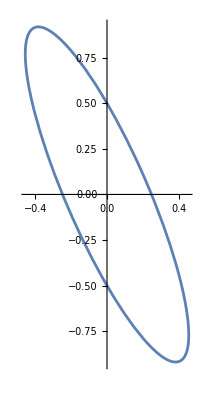

```mathematica
ParametricPlot[diamLst2d⟦1⟧Cos[alpha]+diamLst2d⟦2⟧Sin[alpha],{alpha,0,2π}]
```

```mathematica
area2d=Sin[diamAngle](Times@@diamNormLst2d)
```

0.229114

```mathematica
dBndOpp=Sqrt[1/Total[((rotMatLst⟦1⟧ᵀ.uVectLst3⟦#⟧)⟦1;;2⟧)^2/diamNormLst2d^2]]&/@Range[2]
```

{0.96598,1.03789}

```mathematica
diamInv
```

{{4.02345,1.75191},{0.298047,-0.961273}}

```mathematica
dBndOpp=Sqrt[1/Total[(diamInv.uVectLst3⟦#⟧⟦1;;2⟧)^2]]&/@Range[2]
```

{0.247863,0.500423}

```mathematica
dBndOpp=Sqrt[1/Total[(diamInv⟦All,#⟧)^2]]&/@Reverse[Range[2]]
```

{0.500423,0.247863}

```mathematica
dBnd=radius area2d/(Sqrt[1/Total[(diamInv⟦All,#⟧)^2]]&/@Reverse[Range[2]])
```

{0.0915683,0.184871}

```mathematica
dBnd=Reverse[area2d/dBndOpp radius]
```

{0.0915683,0.184871}

```mathematica
dBnd=area2d/dBndOpp radius
```

{0.0474366,0.0441501}

```mathematica
xyLstRot2d=(diamInv.xyzLst⟦1;;2⟧)
```

{4.02345 x+1.75191 y,0.298047 x-0.961273 y}

```mathematica
xyLstRot2d=(rotMatLst⟦1⟧.xyzLst)⟦1;;2⟧/.z->0
```

{0.+0.218979 x+0.399088 y,0.+0.0678954 x-0.916548 y}

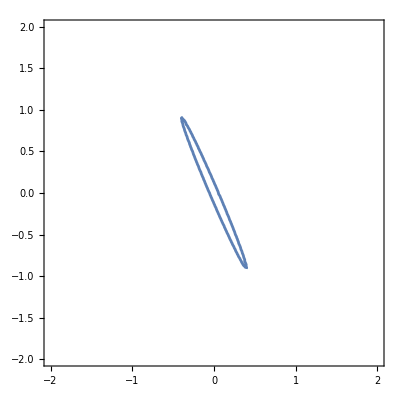

```mathematica
ContourPlot[eqEllipse2d,{x,-2,2},{y,-2,2},AspectRatio->Automatic]
```

```mathematica
eqEllipse2d=Total[xyLstRot2d^2/diamNormLst2d^2//Simplify]==1
```

0.0888912 (1. x-3.22524 y)^2+307.984 (1. x+0.435425 y)^2==1

```mathematica
eqEllipse2d=Total[xyLstRot2d^2/diamNormLst2d^2//Simplify]==1
```

0.00461287 (0.+1. x-13.4994 y)^2+0.912298 (0.+1. x+1.82249 y)^2==1

```mathematica
eqEllipse2d/.y->0//Simplify
```

1. x^2==1.09062

```mathematica
eqEllipse2d/.x->0//Simplify
```

1. y^2==0.258344

```mathematica
Abs[y/.Solve[eqEllipse2d/.x->0]⟦1⟧]
```

0.508276

```mathematica
diamAngle=ArcCos[(Dot@@diamLst2d)]
```

1.54563

```mathematica
ArcCos[(Dot@@diamLst2d)/(Times@@(Norm/@diamLst2d))]180/π
```

83.6967

```mathematica
diamNormLst2d=Norm/@diamLst2d
```

{0.229263,0.999666}

```mathematica
ListPointPlot3D[ellipseSampleLst⟦1,All⟧]
```

-Graphics3D-

```mathematica
radius
```

0.2

```mathematica
ptCenterLst⟦1,1;;2⟧
```

{0.433239,0.479043}

```mathematica
diamLst2d
```

{{0.218979,0.0678954},{0.399088,-0.916548}}

```mathematica
radius diamLst2d
```

{{0.0437959,0.0798176},{0.0135791,-0.18331}}

```mathematica
+{{1,2},{3,4}}
```

Thread::tdlen: Objects of unequal length in {{0.433239,0.479043}}+{{1,2},{3,4}} cannot be combined.

{{0.433239,0.479043}}+{{1,2},{3,4}}

```mathematica
({ptCenterLst⟦1,1;;2⟧,ptCenterLst⟦1,1;;2⟧+#})&/@(radius diamLst2d)
```

{{{0.433239,0.479043},{0.477035,0.55886}},{{0.433239,0.479043},{0.446818,0.295733}}}

```mathematica
(ptCenterLst⟦1,1;;2⟧+{{0,0},#})&/@(radius diamLst2d)
```

{{{0.433239,0.433239},{0.522838,0.55886}},{{0.433239,0.433239},{0.492622,0.295733}}}

```mathematica
Arrow[ptCenterLst⟦1,1;;2⟧+{{0,0},#}&/@radius diamLst2d]
```

Arrow[{{0.0437959,0.0135791},{0.0798176,-0.18331}}]

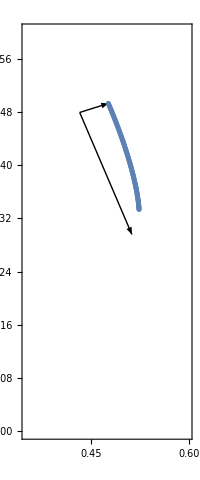

```mathematica
Show[ListPlot[ellipseSampleLst⟦1,1;;100,1;;2⟧,AspectRatio->Automatic],Graphics[Arrow[({ptCenterLst⟦1,1;;2⟧,ptCenterLst⟦1,1;;2⟧+#})&/@(radius diamLst2d)],AspectRatio->1],PlotRange->{{0.35,0.6},{0,0.6}},Frame->True,Axes->False]
```

```mathematica
{ptCenterLst⟦1,1;;2⟧+dBnd}
```

{{0.477117,0.569196}}

```mathematica
radius
```

0.2

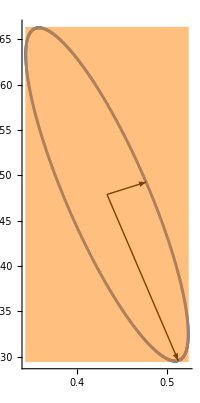

```mathematica
Show[ListPlot[ellipseSampleLst⟦1,All,1;;2⟧,AspectRatio->Automatic],Graphics[Arrow[({ptCenterLst⟦1,1;;2⟧,ptCenterLst⟦1,1;;2⟧+#})&/@(radius diamLst2d)],AspectRatio->1],Graphics[{Opacity[0.5],Orange,Rectangle[ptCenterLst⟦1,1;;2⟧-dBnd,ptCenterLst⟦1,1;;2⟧+dBnd]}],PlotRange->All]
```

```mathematica
radius diamLst2d
```

{{0.0437959,0.0135791},{0.0798176,-0.18331}}

```mathematica
radius diamLst2d
```

{{0.0437959,0.0135791},{0.0798176,-0.18331}}

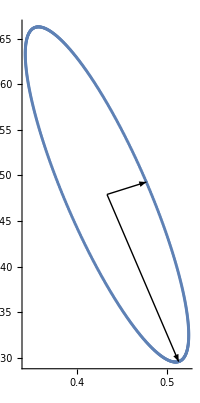

```mathematica
Show[ListPlot[ellipseSampleLst⟦1,All,1;;2⟧,AspectRatio->Automatic],Graphics[Arrow[({ptCenterLst⟦1,1;;2⟧,ptCenterLst⟦1,1;;2⟧+#})&/@(radius diamLst2d)],AspectRatio->1],PlotRange->All]
```

```mathematica
Show[ListPlot[ellipseSampleLst⟦1,All,1;;2⟧,AspectRatio->Automatic],Graphics[Arrow[({ptCenterLst⟦1,1;;2⟧,ptCenterLst⟦1,1;;2⟧+#})&/@(radius diamLst2d)],AspectRatio->1],PlotRange->All]
```

-Graphics-

### Random generation of ellipses

```mathematica
nDimQuart=4;
numPts=20;
(*quartLst=RandomVariate[NormalDistribution[],{numPts,nDimQuart}];*)
ptCenterLst=RandomReal[{0,1},{numPts,nDim3}];
```

```mathematica
radius=0.2;
magMinAxLst=ConstantArray[radius,{numPts,2}];
```

```mathematica
genRotMatLst[numPts_]:=
Module[{nDimQuart=4,quartLst,quartLstNorm,rotMatLst},
quartLst=RandomVariate[NormalDistribution[],{numPts,nDimQuart}];
quartLstNorm=#/Norm[#]&/@quartLst;
rotMatLst=quartToRotMatFunc/@quartLstNorm;
rotMatLst
];
```

```mathematica
(*quartLstNorm=#/Norm[#]&/@quartLst;*)
(*rotMatLst=quartToRotMatFunc/@quartLstNorm;*)
rotMatLst=genRotMatLst[numPts];
```

```mathematica
genAxisMatLst[rotMatLst_,magMinAxLst_]:=
Module[{axisMatLst=rotMatLst},
Do[
axisMatLst⟦All,All,dim⟧=axisMatLst⟦All,All,dim⟧magMinAxLst⟦All,dim⟧;
,{dim,2}];
axisMatLst
]
```

```mathematica
axisMatLst=rotMatLst;
Do[
axisMatLst⟦All,All,dim⟧=axisMatLst⟦All,All,dim⟧magMinAxLst⟦All,dim⟧;
,{dim,2}]
```

```mathematica
xyzLst={x,y,z};
```

```mathematica
(*ellipseSub:=MapThread[Mod[#1.{#3⟦1⟧ Cos[alpha],#3⟦2⟧ Sin[alpha],0}+#2,1]&,{rotMatLst,ptCenterLst,magMinAxLst}];*)
```

```mathematica
genEllipseSampleLstWithFlt[axisMatLst_,ptLst_,numPts_]:=
Module[{ellipseSub,ellipseFuncLst,alphaLst,ellipseSampleLst,ellipseSampleLstFlt,alphaExt},
ellipseSub:=MapThread[Mod[#1.{Cos[alphaExt], Sin[alphaExt],0}+#2,1]&,{axisMatLst,ptLst}];
ellipseFuncLst=Table[Function[alpha,Evaluate[ellipseSub⟦ii⟧/.alphaExt->alpha]],{ii,numPts}];
alphaLst=Range[0,2π,0.01];
ellipseSampleLst=Evaluate[(#/@alphaLst)&/@ellipseFuncLst];
ellipseSampleLstFlt=Flatten[ellipseSampleLst,1];
{ellipseSampleLst,ellipseSampleLstFlt}
];
```

```mathematica
{ellipseSampleLst,ellipseSampleLstFlt}=genEllipseSampleLstWithFlt[axisMatLst,ptCenterLst,numPts];
```

```mathematica
eSub⟦1⟧
```

{Mod[0.344385-0.190544 Cos[alphaExt$89949]+0.0037777 Sin[alphaExt$89949],1],Mod[0.759596+0.0463252 Cos[alphaExt$89949]+0.138224 Sin[alphaExt$89949],1],Mod[0.237998+0.0393319 Cos[alphaExt$89949]-0.144499 Sin[alphaExt$89949],1]}

```mathematica
eFun⟦1⟧[1]
```

{0.244613,0.900937,0.137658}

```mathematica
genEllipseSampleLstWithFlt[axisMatLst,ptCenterLst,numPts]//Trace
```

```mathematica
ellipseSampleLst//Dimensions
```

{20,629,3}

```mathematica
ellipseSampleLst⟦2,1⟧
```

{0.385917,0.942891,0.948762}

```mathematica
ellipseSampleLstFlt//Dimensions
```

{12580,3}

```mathematica
ellipseFuncLst⟦1⟧
```

Function[alpha,{Mod[0.344385-0.190544 Cos[alpha]+0.0037777 Sin[alpha],1],Mod[0.759596+0.0463252 Cos[alpha]+0.138224 Sin[alpha],1],Mod[0.237998+0.0393319 Cos[alpha]-0.144499 Sin[alpha],1]}]

```mathematica
ellipseSub⟦1⟧
```

{Mod[0.344385-0.190544 Cos[alpha]+0.0037777 Sin[alpha],1],Mod[0.759596+0.0463252 Cos[alpha]+0.138224 Sin[alpha],1],Mod[0.237998+0.0393319 Cos[alpha]-0.144499 Sin[alpha],1]}

```mathematica
ellipseFuncLst⟦1⟧
```

Function[alpha,{Mod[0.344385-0.190544 Cos[alpha]+0.0037777 Sin[alpha],1],Mod[0.759596+0.0463252 Cos[alpha]+0.138224 Sin[alpha],1],Mod[0.237998+0.0393319 Cos[alpha]-0.144499 Sin[alpha],1]}]

```mathematica
ellipseSub:=MapThread[Mod[#1.{Cos[alpha], Sin[alpha],0}+#2,1]&,{axisMatLst,ptCenterLst}];
```

```mathematica
ellipseFuncLst=Table[Function[alpha,Evaluate[ellipseSub⟦ii⟧]],{ii,numPts}];
```

```mathematica
alphaLst=Range[0,2π,0.01];
```

```mathematica
ellipseSampleLst=(#/@alphaLst)&/@ellipseFuncLst;
```

```mathematica
ellipseSampleLstFlt=Flatten[ellipseSampleLst,1];
```

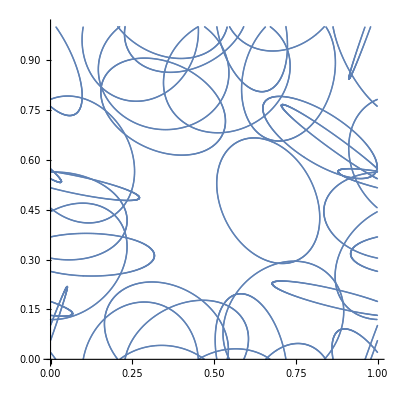

```mathematica
ListPlot[ellipseSampleLstFlt⟦All,1;;2⟧,AspectRatio->1]
```

```mathematica
ListPointPlot3D[ellipseSampleLstFlt,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

#### Boundary boxes in 2d

```mathematica
ptCenter2dLst=ptCenterLst⟦All,1;;2⟧;
```

```mathematica
rotMat2dLst=rotMatLst⟦All,1;;2,1;;2⟧;
rotMat2dLstTrans=Transpose/@rotMat2dLst;
```

```mathematica
diamNorm2dLst=(Norm/@#)&/@rotMat2dLstTrans;
diamCos2dLst=Dot@@##&/@rotMat2dLstTrans/(Times@@#&/@diamNorm2dLst);
diamSin2dLst=Sqrt[1-diamCos2dLst^2];
```

```mathematica
area2dLst=Times@@#&/@diamNorm2dLst diamSin2dLst;
```

```mathematica
rotMatInv2dLst=Inverse/@(rotMat2dLst);
```

```mathematica
dBndLst=Reverse/@(area2dLst/Sqrt[1/Total[rotMatInv2dLst^2,{2}]]);
```

```mathematica
bndRectLst=MapThread[Graphics[{Opacity[0.5],Orange,Rectangle[#1-#2,#1+#2]}]&,{ptCenter2dLst,radius dBndLst}];
```

```mathematica
bndEllipseLst=Transpose[{#1-radius#2,#1+radius#2}]&[ptCenter2dLst,dBndLst];
```

```mathematica
bndRectLst2=MapThread[Graphics[{Opacity[0.5],Orange,Rectangle@@#}]&,{bndEllipseLst}];
```

```mathematica
genAxisMatPtCenter2d[axisMatLst_,ptLst_]:=
Module[{axisMat2dLst,pt2dLst},
axisMat2dLst=axisMatLst⟦All,1;;2,1;;2⟧;
pt2dLst=ptLst⟦All,1;;2⟧;
{axisMat2dLst,pt2dLst}
];
```

```mathematica
{axisMat2dLst,ptCenter2dLst}=genAxisMatPtCenter2d[axisMatLst,ptCenterLst];
```

```mathematica
axisMat2dInvLst=Inverse/@axisMat2dLst;
```

```mathematica
genBndEllipseLst[axisMat2dLst_,pt2dLst_,axisMat2dInvLst_]:=
Module[{axisMat2dTransLst,diamNorm2dLst,diamCos2dLst,diamSin2dLst,area2dLst,dBndLst,bndEllipseLst},
axisMat2dTransLst=Transpose/@axisMat2dLst;
diamNorm2dLst=(Norm/@#)&/@axisMat2dTransLst;diamCos2dLst=Dot@@##&/@axisMat2dTransLst/(Times@@#&/@diamNorm2dLst);
diamSin2dLst=Sqrt[1-diamCos2dLst^2];
area2dLst=Times@@#&/@diamNorm2dLst diamSin2dLst;
dBndLst=Reverse/@(area2dLst/Sqrt[1/Total[axisMat2dInvLst^2,{2}]]);
bndEllipseLst=Transpose[{#1-#2,#1+#2}]&[pt2dLst,dBndLst];
bndEllipseLst
];
```

```mathematica
bndEllipseLst=genBndEllipseLst[axisMat2dLst,ptCenter2dLst,axisMat2dInvLst];
```

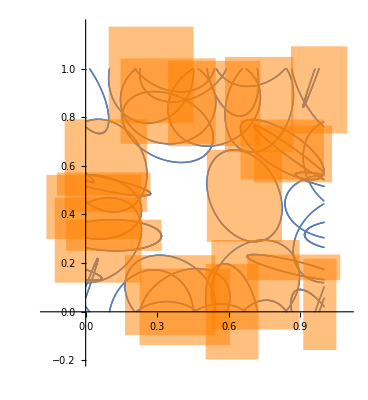

```mathematica
itStop=numPts;
Show[ListPlot[Flatten[ellipseSampleLst⟦1;;itStop,All,1;;2⟧,1],AspectRatio->Automatic],bndRectLst⟦2;;itStop⟧,PlotRange->All]
```

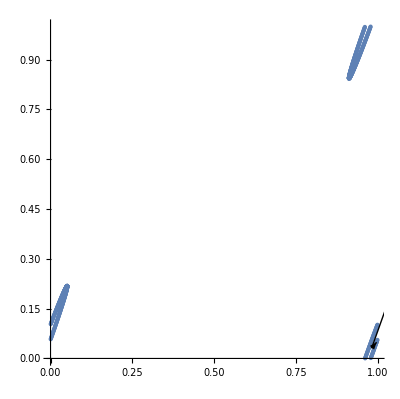

```mathematica
itPick=3;
Show[ListPlot[Flatten[ellipseSampleLst⟦itPick;;itPick,All,1;;2⟧,1],AspectRatio->Automatic],Graphics[Arrow[{ptCenterLst⟦itPick,1;;2⟧,ptCenterLst⟦itPick,1;;2⟧+#}&/@(radius rotMat2dLstTrans⟦itPick⟧)]]]
```

#### Sorting ellipses by boundary box

```mathematica
divNum=128;
```

```mathematica
xyLst2d=xyzLst⟦1;;2⟧;
```

```mathematica
{bndStartLst,bndEndLst}=bndEllipseLst⟦All,#,All⟧&/@Range[2];
```

```mathematica
bndModShLst=Map[If[#<0,1,0]&,bndStartLst,{ArrayDepth[bndStartLst]}];
```

```mathematica
{{bndStartModXLst,bndStartModYLst},{bndEndModXLst,bndEndModYLst}}=
Table[
Module[{bndLst=#},
(bndLst⟦All,iXY⟧=bndLst⟦All,iXY⟧+bndModShLst⟦All,iXY⟧);
bndLst]
,{iXY,2}]&/@{bndStartLst,bndEndLst};
```

```mathematica
xBndStartModXLst=bndStartModXLst⟦All,1⟧;
xBndEndModXLst=bndEndModXLst⟦All,1⟧;
yBndStartModYLst=bndStartModYLst⟦All,2⟧;
yBndEndModYLst=bndEndModYLst⟦All,2⟧;
```

```mathematica
genBndStartEndModXYLst[bndEllipseLst_,pt2dLst_]:=
Module[{bndStartLst,bndEndLst,bndModShLst,bndStartModXLst,bndStartModYLst,bndEndModXLst,bndEndModYLst,xBndStartModXLst,xBndEndModXLst,yBndStartModYLst,yBndEndModYLst,ptCenter2dModLstXYLst},
{bndStartLst,bndEndLst}=bndEllipseLst⟦All,#,All⟧&/@Range[2];
bndModShLst=Map[If[#<0,1,0]&,bndStartLst,{ArrayDepth[bndStartLst]}];
{{bndStartModXLst,bndStartModYLst},{bndEndModXLst,bndEndModYLst}}=
Table[
Module[{bndLst=#},
(bndLst⟦All,iXY⟧=bndLst⟦All,iXY⟧+bndModShLst⟦All,iXY⟧);
bndLst]
,{iXY,2}]&/@{bndStartLst,bndEndLst};
xBndStartModXLst=bndStartModXLst⟦All,1⟧;
xBndEndModXLst=bndEndModXLst⟦All,1⟧;
yBndStartModYLst=bndStartModYLst⟦All,2⟧;
yBndEndModYLst=bndEndModYLst⟦All,2⟧;
ptCenter2dModLstXYLst=
Table[
Module[{ptLst=pt2dLst},
ptLst⟦All,iXY⟧=ptLst⟦All,iXY⟧+bndModShLst⟦All,iXY⟧;
ptLst]
,{iXY,2}];
{xBndStartModXLst,xBndEndModXLst,yBndStartModYLst,yBndEndModYLst,ptCenter2dModLstXYLst}
];
```

```mathematica
{xBndStartModXLst,xBndEndModXLst,yBndStartModYLst,yBndEndModYLst,ptCenter2dModLstXYLst}=genBndStartEndModXYLst[bndEllipseLst,ptCenter2dLst];
```

```mathematica
{ptCenter2dModXLst,ptCenter2dModYLst}=
Table[
Module[{ptLst=ptCenter2dLst},
ptLst⟦All,iXY⟧=ptLst⟦All,iXY⟧+bndModShLst⟦All,iXY⟧;
ptLst]
,{iXY,2}];
```

```mathematica
ptCenter2dModLstXYLst=
Table[
Module[{ptLst=ptCenter2dLst},
ptLst⟦All,iXY⟧=ptLst⟦All,iXY⟧+bndModShLst⟦All,iXY⟧;
ptLst]
,{iXY,2}];
{ptCenter2dModXLst,ptCenter2dModYLst}=ptCenter2dModLstXYLst;
```

```mathematica
getIdFromCoord[x_,divNum_]:=Floor[x divNum];
```

```mathematica
Options[updateCoordIdEnd]={"IsShRight"->False};
updateCoordIdEnd[idQueue_,divNum_,opt:OptionsPattern[]]:=updateCoordIdEnd[idQueue,divNum,opt];
updateCoordIdEnd[idQueue_,divNum_,xBndEndModXLst_,OptionsPattern[]]:=
Module[{xEndNxt,iDivEndNxt,isShRight=OptionValue["IsShRight"]},
xEndNxt=xBndEndModXLst⟦idQueue["Peek"]⟧;
If[isShRight,
xEndNxt=Mod[xEndNxt,1]];
iDivEndNxt=getIdFromCoord[xEndNxt,divNum];
{xEndNxt,iDivEndNxt}
]
```

updateCoordIdEnd

```mathematica
updateSectLst[sectLstVal_,idQueue_,eqLst_,xVal_]:=
Module[{eq,yValLst,sectLst=sectLstVal},
Do[
eq=eqLst⟦iScan⟧;
yValLst=Mod[y/.Solve[eq/.x->xVal],1];
sectLst=Join[sectLst,yValLst];
,{iScan,idQueue["Elements"]}];
sectLst
];
```

```mathematica
Options[updateCoordIdDropOutBnd]=Options[updateCoordIdEnd];
updateCoordIdDropOutBnd[idQueue_,iDiv_,iDivEndNxtVal_,xEndNxtVal_,xBndEndModXLst_,divNum_,OptionsPattern[]]:=
Module[{xEndNxt=xEndNxtVal,iDivEndNxt=iDivEndNxtVal,isShRight=OptionValue["IsShRight"]},
While[!idQueue["EmptyQ"]&&iDiv>iDivEndNxt,
idQueue["Pop"];
If[idQueue["EmptyQ"],Break[]];
{xEndNxt,iDivEndNxt}=updateCoordIdEnd[idQueue,divNum,xBndEndModXLst,"IsShRight"->isShRight];
];
{xEndNxt,iDivEndNxt}
]
```

```mathematica
Options[scanSectFromLst]=Options[updateCoordIdEnd];
(*{"XSh"->0};*)
scanSectFromLst[divNum_,idQueue_,eqLst_,ySectLstVal_,iBegin_,iEnd_,xEndNxtVal_,xBndEndModXLst_,iDivEndNxtVal_,OptionsPattern[]]:=
Module[{xEndNxt=xEndNxtVal,iDivEndNxt=iDivEndNxtVal,ySectLst=ySectLstVal,xVal,xSh(*=OptionValue["XSh"]*),isShRight=OptionValue["IsShRight"]},
If[isShRight,
xSh=1,
xSh=0];
Do[
{xEndNxt,iDivEndNxt}=updateCoordIdDropOutBnd[idQueue,iDiv,iDivEndNxt,xEndNxt,xBndEndModXLst,divNum,"IsShRight"->isShRight];
If[idQueue["EmptyQ"],Break[]];
xVal=xLst⟦iDiv⟧+xSh;
ySectLst⟦iDiv⟧=updateSectLst[ySectLst⟦iDiv⟧,idQueue,eqLst,xVal];
,{iDiv,iBegin,iEnd}];
ySectLst
];
```

```mathematica
xLst=Table[ii/divNum,{ii,1,divNum}];
yLst=xLst;
```

```mathematica
ySectEllipseLst=ConstantArray[{},divNum];
```

```mathematica
genEllipseEqLstXYLst[axisMat2dInvLst_,pt2dModLstXYLst_]:=
Module[{ellipseEqXLst,ellipseEqYLst},
{ellipseEqXLst,ellipseEqYLst}=
Table[
MapThread[(Total[(#1.(xyLst2d-#2))^2]==1)&,{axisMat2dInvLst,ptLst}]
,{ptLst,pt2dModLstXYLst}]
];
```

```mathematica
{ellipseEqXLst,ellipseEqYLst}=genEllipseEqLstXYLst[axisMat2dInvLst,ptCenter2dModLstXYLst];
```

```mathematica
{ellipseEqXLst,ellipseEqYLst}=
Table[
MapThread[(Total[((#1.(xyLst2d-#2))/radius)^2]==1)&,{rotMatInv2dLst,ptLst}]
,{ptLst,{ptCenter2dModXLst,ptCenter2dModYLst}}];
```

```mathematica
idStartSortedLst=Ordering[xBndStartModXLst];
```

```mathematica
idScanningLst=CreateDataStructure["PriorityQueue",{},xBndEndModXLst⟦#1⟧>xBndEndModXLst⟦#2⟧&];
```

```mathematica
idScanningWrapLst=CreateDataStructure["PriorityQueue",{},xBndEndModXLst⟦#1⟧>xBndEndModXLst⟦#2⟧&];
```

```mathematica
updateCoordIdEnd[idScanningLst,divNum,xBndEndModXLst]
```

{0.452294,57}

```mathematica
ySectEllipseLst2=genYSectEllipseLst[divNum,numPts,idScanningLst,idStartSortedLst,xBndStartModXLst,xBndEndModXLst,ellipseEqXLst];
```

```mathematica
xSectEllipseLst2=genXSectEllipseLst[numPts,yBndStartModYLst,yBndEndModYLst,ellipseEqYLst];
```

```mathematica
ySectEllipseLst2
```

1

```mathematica
xSectEllipseLst2
```

```mathematica
genYSectEllipseLst[divNum_,numPts_,idScanningLst_,idStartSortedLst_,xBndStartModXLst_,xBndEndModXLst_,ellipseEqXLst_]:=
Module[{ySectEllipseLst,numPtsPart,iSorted,xStart,xStartNxt,iDivStart,xEndNxt,iDivEndNxt,iDivPreStartNxt},
ySectEllipseLst=ConstantArray[{},divNum];
idScanningLst["DropAll"];
numPtsPart=numPts;
Do[
iSorted=idStartSortedLst⟦iBnd⟧;
xStart=xBndStartModXLst⟦iSorted⟧;
xStartNxt=If[iBnd==numPtsPart,1,xBndStartModXLst⟦idStartSortedLst⟦iBnd+1⟧⟧];
idScanningLst["Push",iSorted];
iDivStart=getIdFromCoord[xStart,divNum]+1;
{xEndNxt,iDivEndNxt}=updateCoordIdEnd[idScanningLst,divNum,xBndEndModXLst];
iDivPreStartNxt=Min[getIdFromCoord[xStartNxt,divNum],divNum];
ySectEllipseLst=scanSectFromLst[divNum,idScanningLst,ellipseEqXLst,ySectEllipseLst,iDivStart,iDivPreStartNxt,xEndNxt,xBndEndModXLst,iDivEndNxt];
,{iBnd,numPtsPart}];
If[!idScanningLst["EmptyQ"],
{xEndNxt,iDivEndNxt}=updateCoordIdEnd[idScanningLst,divNum,xBndEndModXLst,"IsShRight"->True];
(*idScanningWrapLst=idScanningLst["Elements"];*)
ySectEllipseLst=scanSectFromLst[idScanningLst,ellipseEqXLst,ySectEllipseLst,1,divNum,xEndNxt,xBndEndModXLst,iDivEndNxt,"IsShRight"->True];
];
ySectEllipseLst=Sort/@ySectEllipseLst;
ySectEllipseLst
];
```

```mathematica
genXSectEllipseLst[numPts_,yBndStartModYLst_,yBndEndModYLst_,ellipseEqYLst_]:=
Module[{xSectEllipseLst},
xSectEllipseLst={};
Do[
If[yBndStartModYLst⟦iBnd⟧<1&&yBndEndModYLst⟦iBnd⟧>1,
xSectEllipseLst=xSectEllipseLst~Join~Mod[(x/.Solve[ellipseEqYLst⟦iBnd⟧/.y->1]),1];
]
,{iBnd,numPts}];
xSectEllipseLst=Sort[xSectEllipseLst];
xSectEllipseLst
]
```

```mathematica
ySectEllipseLst=ConstantArray[{},divNum];
idScanningLst["DropAll"];
numPtsPart=numPts;
Do[
iSorted=idStartSortedLst⟦iBnd⟧;
xStart=xBndStartModXLst⟦iSorted⟧;
xStartNxt=If[iBnd==numPtsPart,1,xBndStartModXLst⟦idStartSortedLst⟦iBnd+1⟧⟧];
idScanningLst["Push",iSorted];
iDivStart=getIdFromCoord[xStart,divNum]+1;
{xEndNxt,iDivEndNxt}=updateCoordIdEnd[idScanningLst,divNum];
iDivPreStartNxt=Min[getIdFromCoord[xStartNxt,divNum],divNum];
ySectEllipseLst=scanSectFromLst[idScanningLst,ellipseEqXLst,ySectEllipseLst,iDivStart,iDivPreStartNxt,xEndNxt,iDivEndNxt];
,{iBnd,numPtsPart}];
If[!idScanningLst["EmptyQ"],
{xEndNxt,iDivEndNxt}=updateCoordIdEnd[idScanningLst,divNum,"IsShRight"->True];
idScanningWrapLst=idScanningLst["Elements"];
ySectEllipseLst=scanSectFromLst[idScanningLst,ellipseEqXLst,ySectEllipseLst,1,divNum,xEndNxt,iDivEndNxt,"IsShRight"->True];
];
ySectEllipseLst=Sort/@ySectEllipseLst;
```

```mathematica
xSectEllipseLst={};
idEllipseIn={};
Do[
If[yBndStartModYLst⟦iBnd⟧<1&&yBndEndModYLst⟦iBnd⟧>1,
AppendTo[idEllipseIn,iBnd];
xSectEllipseLst=xSectEllipseLst~Join~Mod[(x/.Solve[ellipseEqYLst⟦iBnd⟧/.y->1]),1];
]
,{iBnd,numPts}];
xSectEllipseLst=Sort[xSectEllipseLst];
```

```mathematica
ptSectLst=Table[{xLst⟦iDiv⟧,#}&/@ySectEllipseLst⟦iDiv⟧,{iDiv,divNum}];
ptSectLstFlt=Flatten[ptSectLst,1];
```

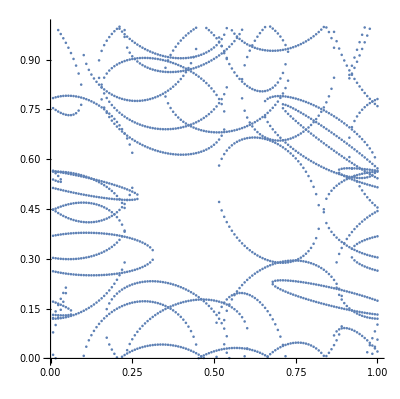

```mathematica
ListPlot[ptSectLstFlt,PlotRange->All,AspectRatio->Automatic]
```

#### Painting Zak phase according to the boundary

```mathematica
genPaintArr[ySectLst_,xSectLst_,divNum_]:=
Module[{paintArr,paintArrLast,paintXLst,iBnd,zakVal,yBndVal,xBndVal},
paintArr=ConstantArray[False,ConstantArray[divNum,2]];
paintXLst=ConstantArray[False,divNum];
Do[
iBnd=1;
zakVal=False;
yBndVal=If[iBnd>Length[ySectLst⟦ii⟧],1,ySectLst⟦ii,iBnd⟧];
Do[
If[jj>divNum yBndVal,
iBnd++;
yBndVal=If[iBnd>Length[ySectLst⟦ii⟧],1,ySectLst⟦ii,iBnd⟧];
zakVal=!zakVal;
];
paintArr⟦ii,jj⟧=zakVal;
,{jj,divNum}]
,{ii,divNum}];
iBnd=1;
xBndVal=If[iBnd>Length[xSectLst],1,xSectLst⟦iBnd⟧];
zakVal=False;
Do[
While[ii>divNum xBndVal,
iBnd++;
xBndVal=If[iBnd>Length[xSectLst],1,xSectLst⟦iBnd⟧];
zakVal=!zakVal;
];
paintXLst⟦ii⟧=zakVal;
,{ii,divNum}];
paintArrLast= paintArr;
Do[paintArrLast⟦ii⟧=Xor[#,paintXLst⟦ii⟧]&/@paintArr⟦ii⟧;
,{ii,divNum}];
paintArrLast
];
```

```mathematica
paintArrLast=genPaintArr[ySectEllipseLst,xSectEllipseLst,divNum];
```

```mathematica
paintArrLast= paintArr;
Do[paintArrLast⟦ii⟧=Xor[#,paintXLst⟦ii⟧]&/@paintArr⟦ii⟧;
,{ii,divNum}]
```

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLast/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLast/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm]
```

-Graphics-

```mathematica
ListPlot[ellipseSampleLstFlt⟦All,1;;2⟧,AspectRatio->1]
```

-Graphics-

## Correlation function

```mathematica
dArea=1/divNum^2;
```

```mathematica
dArea=1/divNum;
```

```mathematica
autoCorr[arr_]:=Re[InverseFourier[Abs[Fourier[arr]]^2]];
```

```mathematica
genPaintCorr[paintArr_,divNum_]:=
Module[{dArea=1/divNum,paintCorr},
paintCorr=dArea autoCorr[paintArr/.subBoolIntMCLoops];
paintCorr
];
```

```mathematica
paintCorr=genPaintCorr[paintArrLast,divNum];
```

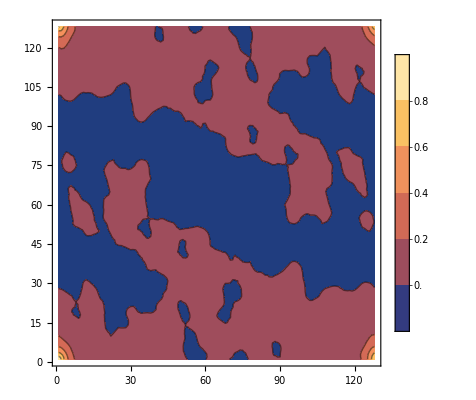

```mathematica
ListContourPlot[paintCorr,PlotRange->All,PlotLegends->Automatic]
```

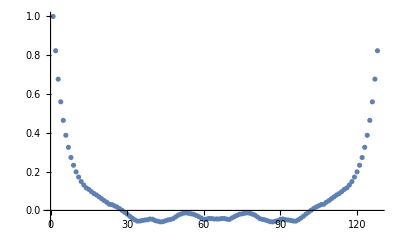

```mathematica
ListPlot[paintCorr⟦All,1⟧,PlotRange->All]
```

## In functions

```mathematica
nDimQuart=4;
numPts=20;
(*quartLst=RandomVariate[NormalDistribution[],{numPts,nDimQuart}];*)
ptCenterLst=RandomReal[{0,1},{numPts,nDim3}];
```

```mathematica
calcEllipsesZak[numPts_,radius_,divNum_]:=
Module[{nDim3=3,ptCenterLst,rotMatLst,magMinAxLst,axisMatLst,ellipseSampleLst,ellipseSampleLstFlt,axisMat2dLst,ptCenter2dLst,axisMat2dInvLst,bndEllipseLst,xBndStartModXLst,xBndEndModXLst,yBndStartModYLst,yBndEndModYLst,ptCenter2dModLstXYLst,ellipseEqXLst,ellipseEqYLst,idStartSortedLst,idScanningLst,idScanningWrapLst,ySectEllipseLst,xSectEllipseLst,paintArr,paintCorr},
ptCenterLst=RandomReal[{0,1},{numPts,nDim3}];
rotMatLst=genRotMatLst[numPts];
magMinAxLst=ConstantArray[radius,{numPts,2}];
axisMatLst=genAxisMatLst[rotMatLst,magMinAxLst];
{ellipseSampleLst,ellipseSampleLstFlt}=genEllipseSampleLstWithFlt[axisMatLst,ptCenterLst,numPts];
{axisMat2dLst,ptCenter2dLst}=genAxisMatPtCenter2d[axisMatLst,ptCenterLst];
axisMat2dInvLst=Inverse/@axisMat2dLst;
bndEllipseLst=genBndEllipseLst[axisMat2dLst,ptCenter2dLst,axisMat2dInvLst];
{xBndStartModXLst,xBndEndModXLst,yBndStartModYLst,yBndEndModYLst,ptCenter2dModLstXYLst}=genBndStartEndModXYLst[bndEllipseLst,ptCenter2dLst];
{ellipseEqXLst,ellipseEqYLst}=genEllipseEqLstXYLst[axisMat2dInvLst,ptCenter2dModLstXYLst];
idStartSortedLst=Ordering[xBndStartModXLst];
idScanningLst=CreateDataStructure["PriorityQueue",{},xBndEndModXLst⟦#1⟧>xBndEndModXLst⟦#2⟧&];
idScanningWrapLst=CreateDataStructure["PriorityQueue",{},xBndEndModXLst⟦#1⟧>xBndEndModXLst⟦#2⟧&];
ySectEllipseLst=genYSectEllipseLst[divNum,numPts,idScanningLst,idStartSortedLst,xBndStartModXLst,xBndEndModXLst,ellipseEqXLst];
xSectEllipseLst=genXSectEllipseLst[numPts,yBndStartModYLst,yBndEndModYLst,ellipseEqYLst];
paintArr=genPaintArr[ySectEllipseLst,xSectEllipseLst,divNum];
paintCorr=genPaintCorr[paintArr,divNum];
{paintArr,paintCorr,ellipseSampleLstFlt,axisMatLst}
];
```

```mathematica
genCorrFitModel[corrArr_]:=
Module[{model,xLst,div,divHalf,divStop,corrLenRaw,divStopRatio=2.5,corrLen},
div=Length[corrArr⟦1⟧];
xLst=Range[0.5,div-0.5]/div;
divHalf=IntegerPart[div/2];
model=NonlinearModelFit[{xLst,corrArr⟦1⟧}ᵀ⟦1;;divHalf⟧,a Exp[-x/b]+c,{{b,0.1},{a,1},{c,0}},x];
corrLenRaw=model["ParameterTableEntries"]⟦1,1⟧;
divStop=ResourceFunction["BinarySearch"][xLst,Max[Min[0.4,divStopRatio corrLenRaw],10]];
model=NonlinearModelFit[{xLst,corrArr⟦1⟧}ᵀ⟦1;;divStop⟧,a Exp[-x/b]+c,{{b,0.1},{a,1},{c,0}},x];
model
];
```

```mathematica
{paintArr,paintCorr,ellipseSampleLstFlt,axisMatLst2}=calcEllipsesZak[numPts,radius,divNum];
```

```mathematica
axisMatLst2⟦1⟧
```

{{-0.191025,0.0544599,-0.11657},{-0.0539684,-0.192441,-0.036674},{-0.0244301,-0.000714577,0.992505}}

```mathematica
itNum=10;
resultLst=Table[calcEllipsesZak[numPts,radius,divNum],{ii,itNum}];
```

```mathematica
Range[5,50,5];
```

```mathematica
radius=0.2;
```

```mathematica
numPtsLst=Range[5,50,5];
radiusLst=Range[0.1,0.5,0.1];
resultLst=Table[calcEllipsesZak[numPts,radius,divNum],{numPts,numPtsLst},{radius,radiusLst}];
```

```mathematica
numPtsRadiusArr=Table[{nPts,radius},{nPts,numPtsLst},{radius,radiusLst}];
```

```mathematica
idNumPtsRadiusArr=Table[{iNPts,iRadius},{iNPts,Length[numPtsLst]},{iRadius,Length[radiusLst]}];
```

```mathematica
idNumPtsRadiusLst=Flatten[idNumPtsRadiusArr,1];
```

```mathematica
numPtsRadiusArr//Dimensions
```

{10,5,2}

```mathematica
resultLst//Dimensions
```

{10,5,4}

```mathematica
paintCorrLst=resultLst⟦All,All,2⟧;
paintArrLst=resultLst⟦All,All,1⟧;
```

```mathematica
paintCorrLst//Dimensions
```

{10,5,128,128}

```mathematica
paintFitModelLst=Map[genCorrFitModel,paintCorrLst,{2}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

General::munfl: Exp[-712.057] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
corrLenLst=Map[#["ParameterTableEntries"]⟦1,1⟧&,paintFitModelLst,{2}];
```

General::munfl: Exp[-712.363] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.581] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-734.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
corrLenLst//Dimensions
```

{10,5}

```mathematica
ListPlot3D[corrLenLst,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
paintFitModelLst//Dimensions
```

{10,5}

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
paintCorr=Table[resultLst⟦ii,2⟧,{ii,itNum}];
```

```mathematica
paintCorr//Dimensions
```

{10,128,128}

```mathematica
paintCorrLst=Table[genPaintCorr[resultLst⟦iNum,iR,1⟧,divNum],{iNum,Length[numPtsLst]},{iR,Length[radiusLst]}];
```

```mathematica
paintCorrLst//Dimensions
```

{10,5,128,128}

```mathematica
paintCorrMean=Mean[paintCorr];
```

```mathematica
paintCorrMean//Dimensions
```

{128,128}

```mathematica
{numPtsLst⟦7⟧,radiusLst⟦2⟧}
```

{35,0.2}

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦7,2⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@paintArr/.subBoolIntPlot]
```

-Graphics-

```mathematica
RandomReal[{0,1},3]
```

{0.427824,0.18523,0.462966}

```mathematica
xLst=Range[0.5,128-0.5]/128;
```

```mathematica
xLst//Dimensions
```

{128}

```mathematica
{xLst,paintCorrLst⟦1,4,1⟧}ᵀ//Dimensions
```

{128,2}

```mathematica
Length[paintCorrLst⟦1,4⟧⟦1⟧]
```

128

```mathematica
modelTest1=genCorrFitModel[paintCorrLst⟦1,4⟧/.subBoolIntPlot];
```

```mathematica
modelTest1⟦1⟧["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0671601 | 0.000517785 | 129.706 | 6.53536×10^-27
a | 1.01621 | 0.00247573 | 410.467 | 2.05623×10^-35
c | 0.0382794 | 0.0029578 | 12.9419 | 3.14086×10^-10

```mathematica
modelTestTest=NonlinearModelFit[{xLst,Exp[-xLst]}ᵀ,a Exp[-b x]+c,{b,a,c},x];
```

```mathematica
modelTestTest["Function"]
```

-1.33227×10^-15+1. ⅇ^(-1. #1)&

```mathematica
Show[{Plot[modelTestTest["Function"][x],{x,0,128}],ListPlot[{xLst,Exp[-xLst]}ᵀ]},PlotRange->All]
```

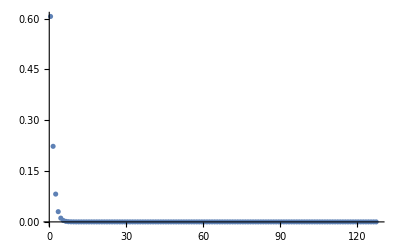

```mathematica
Show[{Plot[modelTestTest["Function"][x],{x,0,128}],ListPlot[{xLst,Exp[-xLst]}ᵀ]},PlotRange->All]
```

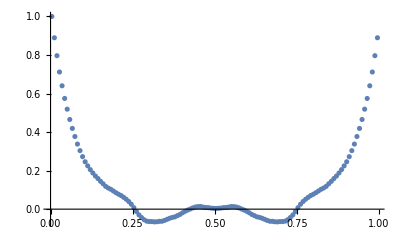

```mathematica
ListPlot[{xLst,paintCorrLst⟦1,4,1⟧}ᵀ]
```

```mathematica
modelTest=NonlinearModelFit[{xLst,paintCorrLst⟦1,4,1⟧}ᵀ⟦1;;64⟧,a Exp[-x/b]+c,{{b,0.1},{a,1},{c,0}},x];
```

```mathematica
modelTest["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0797738 | 0.00268823 | 29.6753 | 5.90074×10^-38
a | 1.05935 | 0.0188205 | 56.2867 | 2.73337×10^-54
c | -0.0315014 | 0.0060888 | -5.17366 | 2.70289×10^-6

```mathematica
modelTest["ParameterTableEntries"]⟦1,1⟧
```

0.0797738

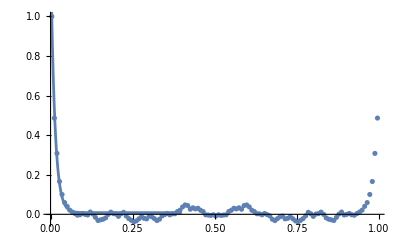

```mathematica
Show[{ListPlot[{xLst,paintCorrLst⟦#1,#2⟧⟦1⟧}ᵀ,PlotRange->All],Plot[paintFitModelLst⟦#1,#2⟧["Function"][x],{x,0,0.4},PlotRange->All]}]&[10,2]
```

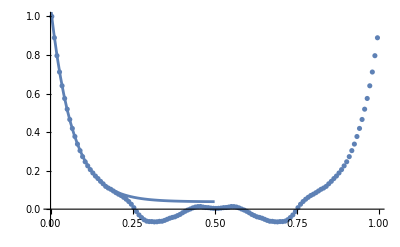

```mathematica
Show[{ListPlot[{xLst,paintCorrLst⟦1,4,1⟧}ᵀ,PlotRange->All],Plot[modelTest1⟦1⟧["Function"][x],{x,0,0.5},PlotRange->All]}]
```

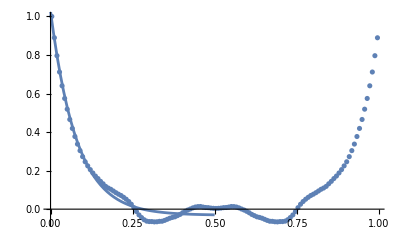

```mathematica
Show[{ListPlot[{xLst,paintCorrLst⟦1,4,1⟧}ᵀ,PlotRange->All],Plot[modelTest["Function"][x],{x,0,0.5},PlotRange->All]}]
```

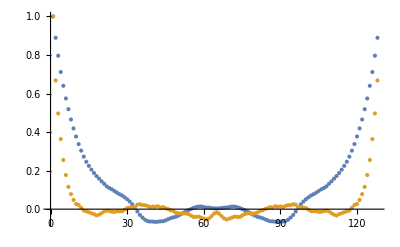

```mathematica
ListPlot[{paintCorrLst⟦1,4,1⟧,paintCorrLst⟦7,2,1⟧},PlotRange->All]
```

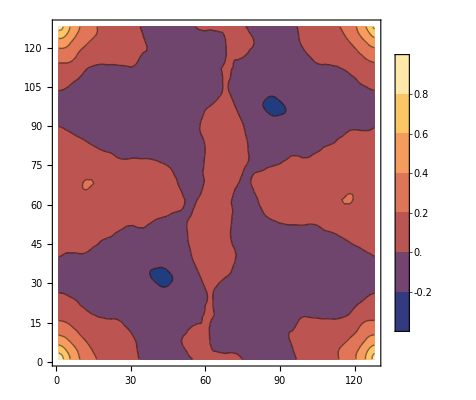

```mathematica
ListContourPlot[paintCorrLst⟦1,4⟧,PlotRange->All,PlotLegends->Automatic]
```

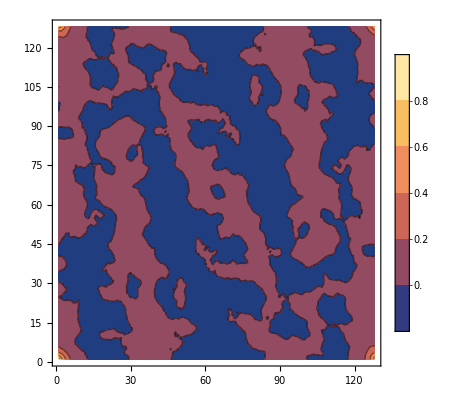

```mathematica
ListContourPlot[paintCorrLst⟦7,2⟧,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
ListContourPlot[paintCorrMean,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[paintCorr,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## D-wave spherical harmonics

```mathematica
Plot3D[{(x y)/(√(x^2+y^2)),(x^2-y^2)/(2 √(x^2+y^2))},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
theta=10π/10;
Plot3D[Cos[theta](x y)/(x^2+y^2)+Sin[theta](x^2-y^2)/(2(x^2+y^2)),{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
divNum=64
```

```mathematica
xLst=Range[0.5,divNum-0.5]/divNum;
yLst=xLst;
```

```mathematica
yGrd=ConstantArray[yLst,divNum];
xGrd=ConstantArray[xLst,divNum]ᵀ;
```

```mathematica
{xLstMod,yLstMod}=(Mod[#+0.5,1]-0.5&)/@{xLst,yLst};
```

```mathematica
yGrdMod=ConstantArray[yLstMod,divNum];
xGrdMod=ConstantArray[xLstMod,divNum]ᵀ;
```

```mathematica
xLst
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5,70.5,71.5,72.5,73.5,74.5,75.5,76.5,77.5,78.5,79.5,80.5,81.5,82.5,83.5,84.5,85.5,86.5,87.5,88.5,89.5,90.5,91.5,92.5,93.5,94.5,95.5,96.5,97.5,98.5,99.5,100.5,101.5,102.5,103.5,104.5,105.5,106.5,107.5,108.5,109.5,110.5,111.5,112.5,113.5,114.5,115.5,116.5,117.5,118.5,119.5,120.5,121.5,122.5,123.5,124.5,125.5,126.5,127.5}

```mathematica
xLstMod
```

{0.00390625,0.0117188,0.0195313,0.0273438,0.0351563,0.0429688,0.0507813,0.0585938,0.0664063,0.0742188,0.0820313,0.0898438,0.0976563,0.105469,0.113281,0.121094,0.128906,0.136719,0.144531,0.152344,0.160156,0.167969,0.175781,0.183594,0.191406,0.199219,0.207031,0.214844,0.222656,0.230469,0.238281,0.246094,0.253906,0.261719,0.269531,0.277344,0.285156,0.292969,0.300781,0.308594,0.316406,0.324219,0.332031,0.339844,0.347656,0.355469,0.363281,0.371094,0.378906,0.386719,0.394531,0.402344,0.410156,0.417969,0.425781,0.433594,0.441406,0.449219,0.457031,0.464844,0.472656,0.480469,0.488281,0.496094,-0.496094,-0.488281,-0.480469,-0.472656,-0.464844,-0.457031,-0.449219,-0.441406,-0.433594,-0.425781,-0.417969,-0.410156,-0.402344,-0.394531,-0.386719,-0.378906,-0.371094,-0.363281,-0.355469,-0.347656,-0.339844,-0.332031,-0.324219,-0.316406,-0.308594,-0.300781,-0.292969,-0.285156,-0.277344,-0.269531,-0.261719,-0.253906,-0.246094,-0.238281,-0.230469,-0.222656,-0.214844,-0.207031,-0.199219,-0.191406,-0.183594,-0.175781,-0.167969,-0.160156,-0.152344,-0.144531,-0.136719,-0.128906,-0.121094,-0.113281,-0.105469,-0.0976563,-0.0898438,-0.0820313,-0.0742188,-0.0664063,-0.0585938,-0.0507813,-0.0429688,-0.0351563,-0.0273438,-0.0195313,-0.0117188,-0.00390625}

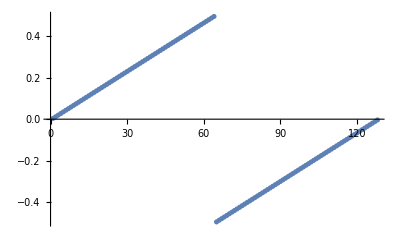

```mathematica
ListPlot[xLstMod]
```

```mathematica
gaussArr=Exp[(-(xGrd^2+yGrd^2))/0.05];
```

```mathematica
gaussArrMod=Exp[(-(xGrdMod^2+yGrdMod^2))/0.05];
```

```mathematica
gaussArrCyc=gaussArr+Reverse[gaussArr]+Reverse[gaussArrᵀ]ᵀ+Reverse[Reverse[gaussArrᵀ]ᵀ];
```

```mathematica
ListPlot3D[gaussArrCyc]
```

-Graphics3D-

```mathematica
ListPlot3D[gaussArr]
```

-Graphics3D-

```mathematica
dWave1=(x y)/(x^2+y^2)/.{x->xGrdMod,y->yGrdMod};
```

```mathematica
dWave2=(x^2-y^2)/(2(x^2+y^2))/.{x->xGrdMod,y->yGrdMod};
```

```mathematica
ListPlot3D[dWave1]
```

-Graphics3D-

```mathematica
maskPinch=dWave1  gaussArrCyc;
```

```mathematica
maskPinch2=dWave2  gaussArrCyc;
```

```mathematica
ListPlot3D[dWave1 gaussArrCyc,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[dWave1 gaussArr]
```

-Graphics3D-

```mathematica
xLst//Dimensions
```

{128}

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦7,2⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
paintArrLst⟦1,4⟧//Dimensions
```

{128,128}

```mathematica
subBoolIntMCLoops
```

{False→1,True→-1}

```mathematica
paintArrFFT=Fourier[paintArrLst⟦1,4⟧/.subBoolIntMCLoops];
```

```mathematica
maskPinchFFT=Fourier[maskPinch];
```

```mathematica
maskPinch2FFT=Fourier[maskPinch2];
```

```mathematica
maskedFFT=paintArrFFT* maskPinchFFT;
```

```mathematica
maskedFFT2=paintArrFFT* maskPinch2FFT;
```

```mathematica
masked=InverseFourier[maskedFFT];
```

```mathematica
masked2=InverseFourier[maskedFFT2];
```

```mathematica
masked//Dimensions
```

{128,128}

```mathematica
Re[1+3ⅈ]
```

1

```mathematica
maskedReal=Re[masked];
```

```mathematica
masked2Real=Re[masked2];
```

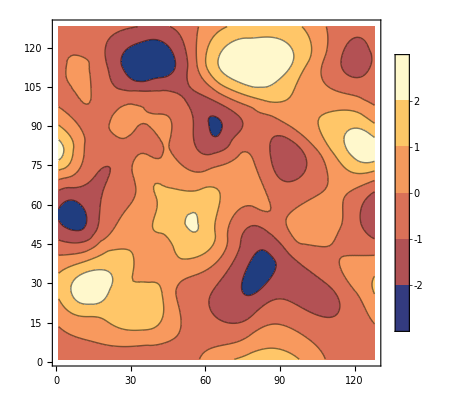

```mathematica
ListContourPlot[maskedReal,PlotLegends->Automatic]
```

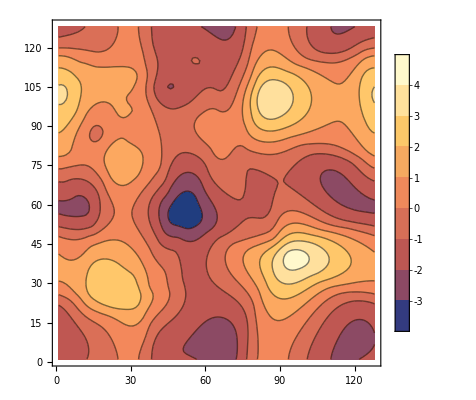

```mathematica
ListContourPlot[masked2Real,PlotLegends->Automatic]
```

```mathematica
maskedAbs=√(Abs[masked]^2+Abs[masked2]^2);
```

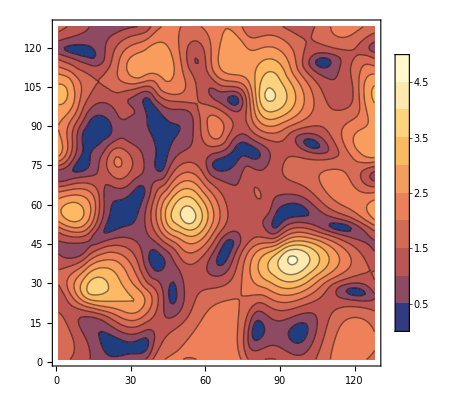

```mathematica
ListContourPlot[maskedAbs,PlotLegends->Automatic]
```

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None,ImageSize->10cm,BaseStyle->texStyle]
```

-Graphics-

```mathematica
ListPlot3D[maskedAbs,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ListPlot3D[maskedReal]
```

-Graphics3D-

## Pinching point identification practice

### Pre Filter Functions

```mathematica
xMidLstFun[divNum_]:=Range[0.5,divNum-0.5]/divNum;
```

```mathematica
mod0Centered[val_,modVal_]:=Mod[val+modVal/2,modVal]-modVal/2;
```

### Gaussian and D-wave filter functions

```mathematica
rSig=0.05;
```

```mathematica
Options[genGaussArr]={"cutoffRatio"->1};
genGaussArr[xGrd_,yGrd_,rSig_,OptionsPattern[]]:=
Module[{cutRatio=OptionValue["cutoffRatio"],cutoff},
cutoff=rSig cutRatio;
Exp[(-(xGrd^2+yGrd^2))/rSig]MapThread[If[#1^2+#2^2>cutoff,0,1]&,{xGrd,yGrd},2]
];
```

```mathematica
genGaussArrSym[gArr_]:=gArr+Reverse[gArr]+Reverse[gArrᵀ]ᵀ+Reverse[Reverse[gArrᵀ]ᵀ];
```

```mathematica
genDWave1[xGrd_,yGrd_]:=(xGrd yGrd)/(xGrd^2+yGrd^2);
genDWave2[xGrd_,yGrd_]:=(xGrd^2-yGrd^2)/(2(xGrd^2+yGrd^2));
```

```mathematica
genDWaveMaskCutoffFft[rSig_,xGrd_,yGrd_,xModGrd_,yModGrd_]:=
Module[{gaussArr,gaussArrSym,dWave1,dWave2,dWaveMaskLst},
gaussArr=genGaussArr[xGrd,yGrd,rSig];
gaussArrSym=genGaussArrSym[gaussArr];
dWave1=genDWave1[xModGrd,yModGrd];
dWave2=genDWave2[xModGrd,yModGrd];
dWaveMaskLst=# gaussArrSym&/@{dWave1,dWave2};
dWaveMaskFftLst=Fourier/@dWaveMaskLst
];
```

### Convolution and FFT

```mathematica
genMaskedAbs[arr_,dWave1Fft_,dWave2Fft_]:=
Module[{arrFft,arrMaskedFftLst,arrMaskedLst,arrMaskedAbs},
arrFft=Fourier[arr];
arrMaskedFftLst=(#*arrFft)&/@{dWave1Fft,dWave2Fft};
arrMaskedLst=InverseFourier/@arrMaskedFftLst;
arrMaskedAbs=√Total[Abs[#]^2&/@arrMaskedLst];
arrMaskedAbs
];
```

### Helpers initialization functions

```mathematica
updateGrd[divNum_]:=
Module[{},
If[divNum!=divNumDetect,
divNumDetect=divNum;
updateGrd[];]
];
```

```mathematica
updateGrd[]:=
Module[{},
xLst=xMidLstFun[divNumDetect];
yLst=xLst;
{xLstMod,yLstMod}=mod0Centered[#,1]&/@{xLst,yLst};
{xGrd,yGrd}=meshGrid[xLst,yLst];
{xModGrd,yModGrd}=meshGrid[xLstMod,yLstMod];
];
```

```mathematica
updateDWaveMaskFft[rSig_]:=
Module[{},
If[rSigDetect!=rSig||Dimensions[dWaveMaskFftLst⟦1⟧]⟦1⟧!=divNumDetect,
rSigDetect=rSig;
updateDWaveMaskFft[]];
];
```

```mathematica
updateDWaveMaskFft[]:=Module[{},
dWaveMaskLst=genDWaveMaskCutoffFft[rSigDetect,xGrd,yGrd,xModGrd,yModGrd];
];
```

### Compute function

```mathematica
calcMaskedAbs[arr_]:=
calcMaskedAbs[arr,rSigDetect];
```

```mathematica
calcMaskedAbs[arr_,rSig_]:=
Module[{},
updateGrd[Dimensions[arr]⟦1⟧];
updateDWaveMaskFft[rSig];
genMaskedAbs[arr,Evaluate[Sequence@@dWaveMaskFftLst]]
];
```

### Initialization

```mathematica
divNumDetect=128;
rSigDetect=0.1;
updateGrd[];
updateDWaveMaskFft[];
```

### Computation

```mathematica
bitMapTest=ConstantArray[-1,{divNum,divNum}];
```

```mathematica
Module[{jStart,jEnd,jTmp},
Do[
jStart=ii;
jEnd=divNum+1-ii;
If[jStart>jEnd,jTmp=jStart;jStart=jEnd;jEnd=jTmp];
Do[
bitMapTest⟦ii,jj⟧=1;
,{jj,jStart,jEnd}]
,{ii,divNum}]
]
```

```mathematica
bitMapTest2=Join[bitMapTest,bitMapTest];
bitMapTest2=Join[bitMapTest2,bitMapTest2,2];
```

```mathematica
bitMapTest2//Dimensions
```

{256,256}

```mathematica
ArrayPlot[Reverse@Transpose@bitMapTest2+1]
```

-Graphics-

```mathematica
divNum2=2divNum;
```

```mathematica
dWave12=genDWave1[xModGrd2,yModGrd2];
dWave22=genDWave2[xModGrd2,yModGrd2];
```

```mathematica
maskPinch12=dWave12 gaussArr2Symm;
maskPinch22=dWave22 gaussArr2Symm;
```

```mathematica
ListPlot3D[dWave12]
```

-Graphics3D-

```mathematica
gaussArr2=genGaussArr[xGrd2,yGrd2,rSig];
```

```mathematica
gaussArr2Symm=genGaussArrSym[gaussArr2];
```

```mathematica
ListPlot3D[gaussArr2,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[gaussArr2Symm,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Reverse@Transpose@bitMapTest+1]
```

-Graphics-

```mathematica
bitMapTestFft=Fourier[bitMapTest];
```

```mathematica
bitMapTestMaskedFft=maskPinchFFT* bitMapTestFft;
bitMapTestMasked2Fft=maskPinch2FFT* bitMapTestFft;
```

```mathematica
bitMapTestMasked=InverseFourier[bitMapTestMaskedFft];
bitMapTestMasked2=InverseFourier[bitMapTestMasked2Fft];
```

```mathematica
bitMapTestMaskedAbs=√(Abs[bitMapTestMasked]^2+Abs[bitMapTestMasked2]^2);
```

```mathematica
ArrayPlot[Reverse@Transpose@Abs[bitMapTestMasked]]
```

-Graphics-

```mathematica
ArrayPlot[Reverse@Transpose@Abs[bitMapTestMasked2]]
```

-Graphics-

```mathematica
128*0.1
```

12.8

```mathematica
ListPlot3D[bitMapTestMaskedAbs,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Reverse@Transpose@Abs[bitMapTestMaskedAbs]]
```

-Graphics-

```mathematica
Join[{{1,2,3},{-1,-2,-3}},{{4,5,6},{-4,-5,-6}}]
```

{{1,2,3},{-1,-2,-3},{4,5,6},{-4,-5,-6}}

```mathematica
Dimensions
```

```mathematica
{bitMapTest2Fft,maskPinch12Fft,maskPinch22Fft}=Fourier[#]&/@{bitMapTest2,maskPinch12,maskPinch22};
```

```mathematica
{maskedBitMap12Fft,maskedBitMap22Fft}=#*bitMapTest2Fft&/@{maskPinch12Fft,maskPinch22Fft};
```

```mathematica
{maskedBitMap12,maskedBitMap22}=InverseFourier/@{maskedBitMap12Fft,maskedBitMap22Fft};
```

```mathematica
maskedBitMapAbs2=√(Abs[maskedBitMap12]^2+Abs[maskedBitMap22]^2);
```

```mathematica
ListPlot3D[maskedBitMapAbs2]
```

-Graphics3D-

```mathematica
ListPlot[Diagonal[bitMapTestMaskedAbs]]
```

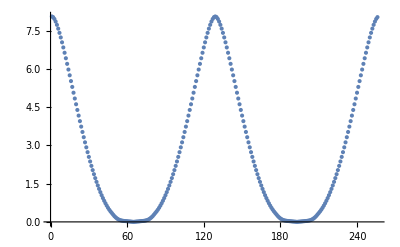

```mathematica
ListPlot[maskedBitMapAbs2⟦128⟧]
```

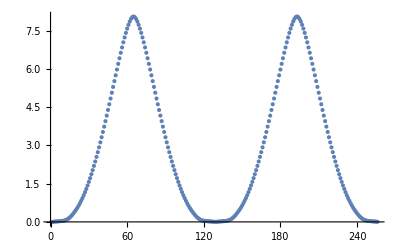

```mathematica
ListPlot[maskedBitMapAbs2⟦64⟧]
```

```mathematica
test1=calcMaskedAbs[maskedBitMapAbs];
```

```mathematica
test1//Dimensions
```

{128,128}

```mathematica
Dimensions[bitMapTest2]⟦1⟧
```

256

```mathematica
test2=calcMaskedAbs⟦bitMapTest2⟧;
```

Part::pkspec1: The expression {{1,1,1,1,1,1,1,1,1,1,«246»},{-1,1,1,1,1,1,1,1,1,1,«246»},{-1,-1,1,1,1,1,1,1,1,1,«246»},{-1,-1,-1,1,1,1,1,1,1,1,«246»},{-1,-1,-1,-1,1,1,1,1,1,1,«246»},{-1,-1,-1,-1,-1,1,1,1,1,1,«246»},{-1,-1,-1,-1,-1,-1,1,1,1,1,«246»},{-1,-1,-1,-1,-1,-1,-1,1,1,1,«246»},{-1,-1,-1,-1,-1,-1,-1,-1,1,1,«246»},{-1,-1,-1,-1,-1,-1,-1,-1,-1,1,«246»},«246»} cannot be used as a part specification.

```mathematica
{maskedBitMapAbs,maskedBitMapAbs2,maskedBitMapAbs2rSigdot05}=calcMaskedAbs[Sequence@@#]&/@{{bitMapTest},{bitMapTest2},{bitMapTest2,0.05}};
```

```mathematica
maskedBitMapAbs//Dimensions
```

{128,128}

```mathematica
ListPlot3D[maskedBitMapAbs,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[maskedBitMapAbs2rSigdot05,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[maskedBitMapAbs2,PlotRange->All]
```

-Graphics3D-

```mathematica
maskedMaxTest2=MaxDetect[maskedBitMapAbs2];
```

```mathematica
maskedMaxTest2rSigDot05=MaxDetect[maskedBitMapAbs2rSigdot05];
```

```mathematica
maskedMaxTest1=MaxDetect[maskedBitMapAbs];
```

```mathematica
ListPlot3D[maskedMaxTest1 maskedBitMapAbs]
```

-Graphics3D-

```mathematica
ListPlot3D[maskedMaxTest]
```

-Graphics3D-

```mathematica
Total[maskedMaxTest2rSigDot05,-1]
```

13

```mathematica
imgTest2=Image[bitMapTest2];
```

```mathematica
ArrayPlot[bitMapTest2/.subBoolIntPlot]
```

-Graphics-

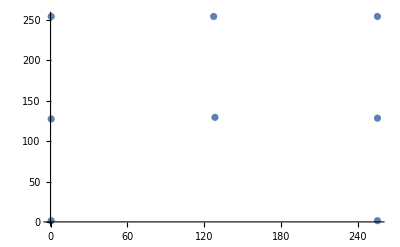

```mathematica
ListPlot[imCornersTest2]
```

```mathematica
ArrayPlot[bitMapTest2⟦33;;96,33;;96⟧+1]
```

-Graphics-

```mathematica
Show[{ArrayPlot[bitMapTest2+1],ListPlot[imCornersTest2,PlotStyle->Red]},ImageSize->8cm]
```

-Graphics-

```mathematica
imCornersTest=ImageCorners[imgTest];
```

```mathematica
imCornersTest2=ImageCorners[imgTest2];
```

```mathematica
imCornersTest2param3=ImageCorners[imgTest2,3,0.01,3];
```

```mathematica
Show[{ArrayPlot[bitMapTest2+1],ListPlot[imCornersTest2param3,PlotStyle->Red]},ImageSize->8cm]
```

-Graphics-

```mathematica
imCornersTest2param3
```

{{255.5,128.5},{66.5,191.5},{194.5,191.5},{66.5,63.5},{194.5,63.5},{127.5,253.5}}

```mathematica
imCornersTest2
```

{{128.5,129.5},{127.5,254.5},{255.5,128.5},{0.5,127.5},{0.5,1.5},{255.5,1.5},{0.5,254.5},{255.5,254.5}}

```mathematica
imCornersTest
```

{{0.5,1.5},{127.5,1.5},{0.5,126.5},{127.5,126.5}}

```mathematica
ListPlot3D[maskedMaxTest2rSigDot05]
```

-Graphics3D-

```mathematica
maskedBitMapAbs2⟦1⟧//Dimensions
```

{256,256}

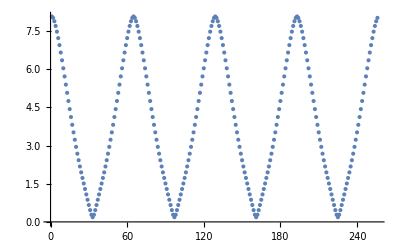

```mathematica
ListPlot[Diagonal[maskedBitMapAbs2]]
```

```mathematica
ans1=Times[Sequence@@dWaveMaskFftLst];
```

```mathematica
ans1//Dimensions
```

{128,128}

```mathematica
ListPlot3D[]
```

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- ({{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«118»},«9»,«118»}})

```mathematica
maskAbsTest=genMaskedAbs[bitMapTest,dWaveMaskFftLst⟦1⟧,dWaveMaskFftLst⟦2⟧];
```

```mathematica
maskAbsTest=genMaskedAbs[bitMapTest,Evaluate[Sequence@@dWaveMaskFftLst]];
```

```mathematica
maskAbsTest=genMaskedAbs[bitMapTest,Sequence@@dWaveMaskFftLst];
```

```mathematica
maskAbsTest//Dimensions
```

{128,128}

```mathematica
maskAbsTest//Dimensions
```

{128,128}

```mathematica
maskAbsTest⟦2,2⟧//Dimensions
```

{128,128}

```mathematica
dWaveMaskFftLst//Dimensions
```

{2,128,128}

```mathematica
divNumDetect
```

256

```mathematica
updateGrd[Dimensions[bitMapTest2]⟦1⟧];
```

```mathematica
divNumDetect
```

256

```mathematica
xLstMod//Dimensions
```

{256}

```mathematica
imgTestCirc=Image[paintArrLst⟦1,4⟧/.subBoolIntPlot];
```

```mathematica
cornersCircTest=ImageCorners[imgTestCirc];
```

```mathematica
cornersCircTestRef=ImageCorners[imgTestCirc,3,0.01,5];
```

```mathematica
cornersCircTestRef2=ImageCorners[Image[paintArrLst⟦7,2⟧/.subBoolIntPlot],3,0.01,5];
```

```mathematica
Length[cornersCircTestRef2]
```

80

```mathematica
Show[ArrayPlot[paintArrLst⟦7,2⟧/.subBoolIntPlot],ListPlot[cornersCircTestRef2+0.5,PlotStyle->Red]]
```

-Graphics-

```mathematica
Length[cornersCircTestRef]
```

25

```mathematica
imCornerFilt=CornerFilter[imgTestCirc];
```

```mathematica
imCornerFilt
```

```mathematica
Show[ImageAdjust[imCornerFilt],ImageSize->10cm]
```

-Graphics-

```mathematica
Show[ArrayPlot[paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None],ListPlot[cornersCircTest,PlotStyle->Red]]
```

-Graphics-

```mathematica
ArrayPlot[paintArrLst⟦1,4⟧/.subBoolIntPlot,PlotRangePadding->None,FrameTicks->Automatic]
```

-Graphics-

```mathematica
cornersCircTestRef
```

{{35.5,39.5},{104.5,73.5},{96.5,110.5},{75.5,52.5},{88.5,103.5},{63.5,84.5},{95.5,95.5},{91.5,27.5},{102.5,93.5},{2.5,79.5},{115.5,24.5},{97.5,87.5},{113.5,84.5},{45.5,103.5},{42.5,45.5},{6.5,114.5},{96.5,21.5},{122.5,111.5},{116.5,112.5},{115.5,54.5},{113.5,43.5},{81.5,40.5},{54.5,78.5},{51.5,72.5},{126.5,76.5}}

### Corner detection test

```mathematica
arrTest=paintArrLst⟦1,4⟧/.subBoolIntPlot;
```

```mathematica
ArrayPlot[arrTest]
```

-Graphics-

```mathematica
imgTest=Image[arrTest];
```

```mathematica
Show[imgTest]
```

-Graphics-

```mathematica
imCornerFiltTest=CornerFilter[imgTest];
```

```mathematica
arrCornerFiltTest=ImageData[imCornerFiltTest];
```

```mathematica
Show[cornerFiltTest,ImageSize->10cm]
```

-Graphics-

```mathematica
ArrayPlot[arrCornerFiltTest,PlotLegends->Automatic]
```

-Graphics-

```mathematica
imCornerFiltTestMax=MaxFilter[imCornerFiltTest,1];
```

```mathematica
imCornerFiltMaxSupp=Binarize[ImageSubtract[imCornerFiltTestMax,imCornerFiltTest],{0,0}];
```

```mathematica
Show[imCornerFiltMaxSupp,ImageSize->10cm]
```

-Graphics-

```mathematica
imCornerFiltPtsAll1=ImageMultiply[imCornerFiltMaxSupp,imCornerFiltTest];
```

```mathematica
arrCornerFiltPtsAll1=ImageData[imCornerFiltPtsAll1];
```

```mathematica
ArrayPlot[arrCornerFiltPtsAll1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Show[Binarize[imCornerFiltPtsAll1,0.01],ImageSize->10cm]
```

-Graphics-

```mathematica
Show[imCornerFiltPtsAll1]
```

-Graphics-

```mathematica
Show[ArrayPlot[paintArrLst⟦1,4⟧/.subBoolIntPlot],ListPlot[cornersCircTestRef-0.5,PlotStyle->Red],PlotRangePadding->None]
```

-Graphics-

```mathematica
Show[ArrayPlot[paintArrLst⟦1,4⟧/.subBoolIntPlot],ListPlot[cornersCircTestRef+0.5,PlotStyle->Red],PlotRangePadding->None]
```

-Graphics-

```mathematica
Show[ArrayPlot[paintArrLst⟦1,4⟧/.subBoolIntPlot],ListPlot[cornersCircTestRef,PlotStyle->Red],PlotRangePadding->None]
```

-Graphics-

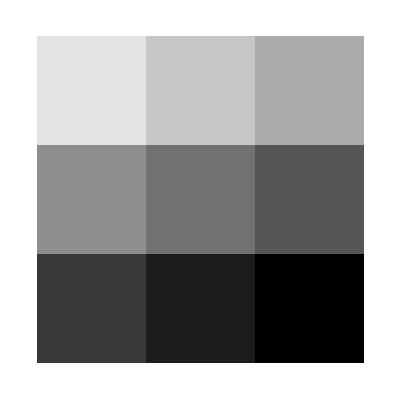

```mathematica
ArrayPlot[{{1,2,3},{4,5,6},{7,8,9}},FrameTicks->Automatic]
```

### Corner detection of the random circle model

```mathematica
meanZakLst=Map[Abs[Total[(#/.subBoolIntMCLoops),-1]/Length[#]^2]&,paintArrLst,{2}];
```

```mathematica
meanZakLst//Dimensions
```

{10,5}

```mathematica
meanZakThres=0.15;
idMeanZakBad=Select[idNumPtsRadiusLst,meanZakLst⟦Sequence@@#⟧>meanZakThres&];
```

```mathematica
idMeanZakBad
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1}}

```mathematica
idNumPtsRadiusArrZakCut=Delete[idNumPtsRadiusArr,idMeanZakBad];
```

```mathematica
idNumPtsRadiusArrZakCut
```

{{{1,4},{1,5}},{{2,3},{2,4},{2,5}},{{3,2},{3,3},{3,4},{3,5}},{{4,2},{4,3},{4,4},{4,5}},{{5,2},{5,3},{5,4},{5,5}},{{6,2},{6,3},{6,4},{6,5}},{{7,2},{7,3},{7,4},{7,5}},{{8,2},{8,3},{8,4},{8,5}},{{9,2},{9,3},{9,4},{9,5}},{{10,2},{10,3},{10,4},{10,5}}}

```mathematica
paintParamsArr=Table[numPtsRadiusArr⟦iPts,iRad⟧~Join~{corrLenLst⟦iPts,iRad⟧,numCornerLst⟦iPts,iRad⟧},{iPts,Length[numPtsLst]},{iRad,Length[radiusLst]}];
```

```mathematica
paintParamsArr1=Table[paintParamsArr⟦iPts,iRad,{3,4,1}⟧,{iPts,Length[numPtsLst]},{iRad,Length[radiusLst]}];
paintParamsArr2=Table[paintParamsArr⟦iPts,iRad,{3,4,2}⟧,{iPts,Length[numPtsLst]},{iRad,Length[radiusLst]}];
```

```mathematica
paintParamsArrOg1=Table[paintParamsArr⟦iPts,iRad,1;;3⟧,{iPts,Length[numPtsLst]},{iRad,Length[radiusLst]}];
paintParamsArrOg2=Table[paintParamsArr⟦iPts,iRad,{1,2,4}⟧,{iPts,Length[numPtsLst]},{iRad,Length[radiusLst]}];
```

```mathematica
{paintParamsArr1Cut,paintParamsArr2Cut}=Delete[#,idMeanZakBad]&/@{paintParamsArr1,paintParamsArr2};
```

```mathematica
{paintParamsArrOg1Cut,paintParamsArrOg2Cut}=Delete[#,idMeanZakBad]&/@{paintParamsArrOg1,paintParamsArrOg2};
```

```mathematica
paintParamsArr1//Dimensions
```

{10,5,3}

```mathematica
{paintParamsLst1Cut,paintParamsLst2Cut}=Flatten[#,1]&/@{paintParamsArr1Cut,paintParamsArr2Cut};
```

```mathematica
paintParamsLst1Cut//Dimensions
```

{37,3}

```mathematica
paintParamsArr//Dimensions
```

{10,5,4}

```mathematica
Flatten[paintParamsArr⟦All,All,1;;3⟧
```

{{{5,0.1,0.0433212},{5,0.2,0.0628298},{5,0.3,0.0600669},{5,0.4,0.0569039},{5,0.5,0.0451492}},{{10,0.1,0.0502489},{10,0.2,0.0411242},{10,0.3,0.0491393},{10,0.4,0.0276381},{10,0.5,0.0233374}},{{15,0.1,0.0392748},{15,0.2,0.0551449},{15,0.3,0.0252941},{15,0.4,0.0229825},{15,0.5,0.0170019}},{{20,0.1,0.0363994},{20,0.2,0.0420423},{20,0.3,0.0240528},{20,0.4,0.0162307},{20,0.5,0.0160716}},{{25,0.1,0.0444929},{25,0.2,0.0282312},{25,0.3,0.0156778},{25,0.4,0.0161747},{25,0.5,0.0103806}},{{30,0.1,0.0390868},{30,0.2,0.0219987},{30,0.3,0.0153236},{30,0.4,0.0114433},{30,0.5,0.00867014}},{{35,0.1,0.0355867},{35,0.2,0.0213741},{35,0.3,0.0120302},{35,0.4,0.00840032},{35,0.5,0.00722151}},{{40,0.1,0.0358104},{40,0.2,0.0164704},{40,0.3,0.0105463},{40,0.4,0.00634995},{40,0.5,0.00163756}},{{45,0.1,0.0279387},{45,0.2,0.0150256},{45,0.3,0.00839265},{45,0.4,0.00459328},{45,0.5,0.000696406}},{{50,0.1,0.0271603},{50,0.2,0.0124143},{50,0.3,0.00675788},{50,0.4,0.000858616},{50,0.5,0.000690918}}}

```mathematica
ListPlot3D[Flatten[paintParamsArr⟦All,All,1;;3⟧,1],ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Flatten[paintParamsArrOg1Cut,1]//Dimensions
```

{37,3}

```mathematica
paintParamsArrOg1Cut//Dimensions
```

{10}

```mathematica
paintParamsArrOg1⟦2;;-1,3,{1,3}⟧//Dimensions
```

{9,2}

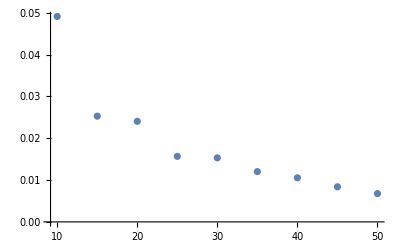

```mathematica
ListPlot[paintParamsArrOg1⟦2;;-1,3,{1,3}⟧]
```

```mathematica
ListPlot3D[Flatten[paintParamsArrOg1Cut,1],ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[paintParamsArrOg2Cut,1],ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
paintParamsLst2CutSorted=Sort[paintParamsLst2Cut,#1⟦3⟧<#2⟦3⟧&];
```

```mathematica
ListPointPlot3D[paintParamsLst2CutSorted⟦1;;8⟧]
```

-Graphics3D-

```mathematica
paintParamsLst2CutSorted
```

{{0.0124143,95,0.2},{0.0150256,95,0.2},{0.0164704,88,0.2},{0.0213741,80,0.2},{0.0219987,77,0.2},{0.0282312,76,0.2},{0.0420423,54,0.2},{0.0551449,39,0.2},{0.00675788,102,0.3},{0.00839265,97,0.3},{0.0105463,106,0.3},{0.0120302,95,0.3},{0.0153236,100,0.3},{0.0156778,85,0.3},{0.0240528,72,0.3},{0.0252941,75,0.3},{0.0491393,34,0.3},{0.000858616,91,0.4},{0.00459328,98,0.4},{0.00634995,83,0.4},{0.00840032,103,0.4},{0.0114433,109,0.4},{0.0161747,86,0.4},{0.0162307,97,0.4},{0.0229825,74,0.4},{0.0276381,65,0.4},{0.0569039,25,0.4},{0.000690918,85,0.5},{0.000696406,80,0.5},{0.00163756,94,0.5},{0.00722151,90,0.5},{0.00867014,90,0.5},{0.0103806,91,0.5},{0.0160716,86,0.5},{0.0170019,81,0.5},{0.0233374,81,0.5},{0.0451492,32,0.5}}

```mathematica
ListPlot3D[paintParamsLst2CutSorted,InterpolationOrder->3,PlotTheme->"FilledSurface"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[paintParamsLst2Cut]
```

-Graphics3D-

```mathematica
ListPointPlot3D[paintParamsLst1Cut]
```

-Graphics3D-

```mathematica
ListPlot3D[meanZakLst,PlotRange->All,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
cornerIdLst=Map[ImageCorners[Image[#/.subBoolIntPlot],3,0.01,5]&,paintArrLst,{2}];
```

```mathematica
numCornerLst=Map[Length,cornerIdLst,{2}];
```

```mathematica
ListPlot3D[numCornerLst,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Show[ArrayPlot[paintArrLst⟦#1,#2⟧/.subBoolIntPlot,PlotRangePadding->None],ListPlot[cornerIdLst⟦#1,#2⟧,PlotStyle->Red]]&[7,5]
```

-Graphics-